# Fully implicit scheme for quasireversible CV

## Using expanding space grid

Version 1.30
copyright © 2002-Year Michael Honeychurch

In this notebook you are asked to load data from the SERM/Data folder. To prepare for this copy the line below to an input cell, replace the file path with the file path for the "Data" folder on your computer and press ⌤

```mathematica
AppendTo[$Path,"(*path to SERM *)/SERM/Data/DigiSimdata"];
```

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.5]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
optionA={
FrameLabel-> {
Style["increment",FontFamily-> "Arial" ,FontSize->  12,FontColor->Black],
Style["√πχ",FontFamily->  "Times New Roman" ,FontSize->   12, FontWeight->   "Plain",FontColor-> Black],
None,
None},
PlotRange-> {{1,All},{-0.5,0.4}},
PlotStyle-> {Red,AbsoluteThickness[0.5]}
};
```

```mathematica
optionB={
FrameLabel->{
StyleForm["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12,FontColor->Black, FontSlant->Italic],
StyleForm["√πχ",FontFamily-> "Times New Roman",FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None},
PlotRange->{{upperLimit+1,lowerLimit-1},{-0.5,0.5}},
PlotStyle->{Red,AbsoluteThickness[0.7]}};
```

```mathematica
optionC={
FrameLabel->{
StyleForm["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
StyleForm["√πχ(at)",FontFamily-> "Times New Roman",FontSize-> 12, FontWeight-> "Plain",FontSlant->"Italic"],
None,
None},
FrameTicks->Automatic,
Joined->{True,True},
PlotStyle-> {Red,Black}
};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeVarDiagonals2];

makeVarDiagonals2[m_Integer,d_][a_]:=
	Module[{x,y,z},
		x=Table[-d*a^(4-2*j),{j,3,m-1}];(*lower diagonal*)
		z=Table[-d*a^(3-2*j),{j,2,m-2}];(*upper diagonal*)
		y=Table[1+(1+a)*d*a^(3-2*j),{j,2,m-1}];(*centre*)
{x,y,z}]
```

```mathematica
Clear[𝔻,a,x,y,z];
{x,y,z}=makeVarDiagonals2[7,𝔻][a]
Table[Switch[j-i,-1,x⟦j⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,4},{j,4}]//MatrixForm
```

{{-𝔻/a^2,-𝔻/a^4,-𝔻/a^6,-𝔻/a^8},{1+((1+a) 𝔻)/a,1+((1+a) 𝔻)/a^3,1+((1+a) 𝔻)/a^5,1+((1+a) 𝔻)/a^7,1+((1+a) 𝔻)/a^9},{-𝔻/a,-𝔻/a^3,-𝔻/a^5,-𝔻/a^7}}

(1+((1+a) 𝔻)/a | -𝔻/a | 0 | 0
-𝔻/a^2 | 1+((1+a) 𝔻)/a^3 | -𝔻/a^3 | 0
0 | -𝔻/a^4 | 1+((1+a) 𝔻)/a^5 | -𝔻/a^5
0 | 0 | -𝔻/a^6 | 1+((1+a) 𝔻)/a^7)

```mathematica
len=Length[y];
SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len]//MatrixForm
```

(1+((1+a) 𝔻)/a | -𝔻/a | 0 | 0 | 0
-𝔻/a^2 | 1+((1+a) 𝔻)/a^3 | -𝔻/a^3 | 0 | 0
0 | -𝔻/a^4 | 1+((1+a) 𝔻)/a^5 | -𝔻/a^5 | 0
0 | 0 | -𝔻/a^6 | 1+((1+a) 𝔻)/a^7 | -𝔻/a^7
0 | 0 | 0 | -𝔻/a^8 | 1+((1+a) 𝔻)/a^9)

## Set Up Solution

```mathematica
Clear[implicitSolveIrrevExpandCV];

implicitSolveIrrevExpandCV[m_Integer,n_Integer,d_,{lowerLimit_,upperLimit_},{ksStar_,α_},a_]:=Module[{x,y,z,len,mat,y1,z1,initial,range,τ,solveNext},

range=2*(upperLimit+Abs[lowerLimit]);
τ=range/(n-1.);

{x,y,z}=makeVarDiagonals2[m,d][a];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];
a1=1;

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2},

ξ=If[k>(n+1)/2,Exp[upperLimit-range+(τ*(k-1))],Exp[upperLimit-(τ*(k-1))]];

tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
b=list[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b⟦-1⟧+=d*a^(5-2*m);
mat⟦1,1⟧=y1-d*tmp*4;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+(tmp2⟦1⟧-tmp2⟦2⟧)*4)*tmp,tmp2,1.}]];

FoldList[solveNext,initial,Range[2,n]]
]
```

## Set Parameter Values

### Variables/ constants

```mathematica
Clear[F,R,T,f,𝒟];

F=N@QuantityMagnitude[UnitConvert@Quantity["FaradayConstant"]];(*Faradays constant*)

R=N@QuantityMagnitude[UnitConvert@Quantity["GasConstant"]];(*gas constant*)

T=298.15;(*temperature*)
f=F/(R*T);
𝒟=1.*^-5;(*diffusion coefficient*)
```

### Electrochemical variables

```mathematica
Clear[upperLimit,lowerLimit,𝕥];
α=0.5 (*transfer coefficient*);

lowerLimit=-15.5766(*limit = f×(E-E^o)*);

upperLimit=11.6435(*limit = f×(E-E^o)*);

𝕥=2.*(upperLimit+Abs[lowerLimit]);
```

### Simulation variables

```mathematica
Clear[n,a,𝔻,temp,m,τ,ksDim,ksStar];

n=Round[𝕥/(.002*f)];(*2mV steps*);

a=1.05;

𝔻=2.;

temp=Solve[∑_(j=1)^(mm-1) a^(j-1)==6*√((𝔻*(1+a)*(n-1))/2),mm,InverseFunctions-> True];

m=mm/.temp⟦1⟧//Ceiling;(*number of spacial grid points*)

τ=𝕥/(n-1) (*calculation of the incremental time/potential step*);

ksDim=0.05;

ksStar=2.*ksDim*Sqrt[𝕥/(𝔻*(n-1))](*dimensionless rate constant*);
```

## Solve

```mathematica
Clear[c];
c=implicitSolveIrrevExpandCV[m,n,𝔻,{lowerLimit,upperLimit},{ksStar,α},a];//Timing
```

{0.000011,Null}

## Plot CV

```mathematica
cv1=Map[(((2+a)*a*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)*√((𝔻*(n-1))/(2*a^2*(1+a)*𝕥)))&,c];
plot1=ListPlot[cv1,optionA]
```

Part::partd: Part specification 53⟦1⟧ is longer than depth of object.

Part::partd: Part specification 53⟦2⟧ is longer than depth of object.

Part::partd: Part specification 53⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of {-15.5766,11.6435} does not exist.

Part::partw: Part 3 of {0.0197477,0.5} does not exist.

Part::partd: Part specification 53.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 53.⟦2⟧ is longer than depth of object.

Part::partd: Part specification 53.⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::lpn: implicitSolveIrrevExpandCV[2.38178 (3.2025 53.⟦1⟧-4.2025 53.⟦2⟧+53.⟦3⟧),2.38178 (3.2025 699.⟦1⟧-4.2025 699.⟦2⟧+699.⟦3⟧),2.38178 (3.2025 2.⟦1⟧-«1»+2.⟦3⟧),«1»,2.38178 (-2.03801+{0.0197477,0.5}⟦3⟧),2.38178 (3.2025 1.05⟦1⟧-4.2025 1.05⟦2⟧+1.05⟦3⟧)] is not a list of numbers or pairs of numbers.

ListPlot[implicitSolveIrrevExpandCV[2.38178 (3.2025 53⟦1⟧-4.2025 53⟦2⟧+53⟦3⟧),2.38178 (3.2025 699⟦1⟧-4.2025 699⟦2⟧+699⟦3⟧),2.38178 (3.2025 2.⟦1⟧-4.2025 2.⟦2⟧+2.⟦3⟧),2.38178 (-98.8159+{-15.5766,11.6435}⟦3⟧),2.38178 (-2.03801+{0.0197477,0.5}⟦3⟧),2.38178 (3.2025 1.05⟦1⟧-4.2025 1.05⟦2⟧+1.05⟦3⟧)],{FrameLabel→{increment,√πχ,None,None},PlotRange→{{1,All},{-0.5,0.4}},PlotStyle→{RGBColor[1, 0, 0],AbsoluteThickness[0.5]}}]

```mathematica
cv2=Table[{If[j>(n+1)/2,upperLimit-𝕥+((j-1)*τ),upperLimit-((j-1)*τ)],cv1⟦j⟧},{j,1,Length[cv1]}];

plot2=ListPlot[cv2,optionB]
```

Part::partd: Part specification 53.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 53.⟦2⟧ is longer than depth of object.

Part::partd: Part specification 53.⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

### Comparison to DigiSim data simulated with 1mV steps

```mathematica
mke=Import["logk-3.dat","Table"];
```

```mathematica
A=1.;
𝒟=1.*^-5;
υ=1.;
c1=1.*^-6;
values=F*A*c1*Sqrt[(𝒟*F*υ)/(R*T)];
mke1=Map[{#⟦1⟧*F/(R*T),-#⟦2⟧/values}&,mke];
```

Part::partd: Part specification 53.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 53.⟦2⟧ is longer than depth of object.

Part::partd: Part specification 53.⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

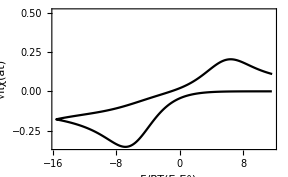

```mathematica
ListPlot[{cv2,mke1},optionC]
```

```mathematica
ListPlot[mke1,optionB,Epilog-> {PointSize[0.01],Blue,Point/@cv2}]
```

-Graphics-